# Mathematica version history

### Mathematica version vs. release date

```mathematica
data0=EntityValue["WolframLanguageSymbol",{"DateIntroduced","VersionIntroduced"}];
data1=Composition[
Cases[#,{_DateObject,_?NumericQ}]&
][data0];
```

```mathematica
frameTick[arg_]:=Row[{arg,Invisible[arg]},""];
```

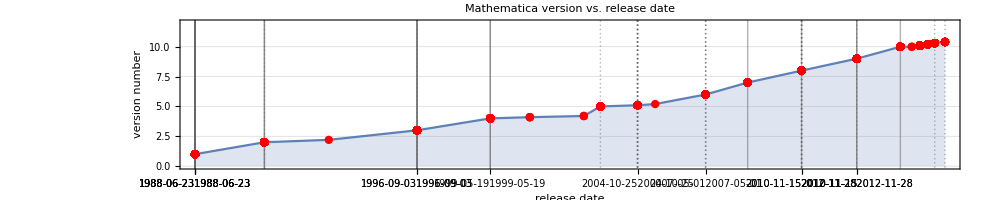

```mathematica
DateListPlot[data1,Mesh->All,PlotTheme->"Detailed",MeshStyle->Red,Filling->Bottom,DateTicksFormat->{"Year","-","Month","-","Day"},FrameTicks->{{Automatic,Automatic},{{#,frameTick@Rotate[Style[#,FontSize-> 8]& @ DateString[#,{"Year","-","Month","-","Day"}],Pi/4]}&/@data1[[All,1]],Automatic}},ImageSize->1000,AspectRatio->1/5,FrameLabel-> {"release date","version number"},PlotRange-> {0,12},PlotLabel-> "Mathematica version vs. release date"]
```

## References

https://www.quora.com/When-will-Mathematica-11-be-released